```mathematica
stations=Import["C:\\Users\\Devon\\Documents\\M3\\moodys-data\\scripts\\stations.txt","Words"]
```

{8723970,8779770,8574680,8461490,8661070,8577330,8594900,9449424,9450460,1630000,8545240,8467150,9410660,8728690,8665530,8770570,9410580,8771510,1612340,8573364,8418150,9418767,9451600,8726724,9453220,9439040,8658120,8413320,9751639,8410140,9449880,9444900,9443090,8723170,8774770,8637624,8726520,8779750,8652587,8443970,9751401,8635150,9410230,9415144,8449130,8519483,9447130,8737048,9412110,8722670,8557380,8419870,8571892,8514560,1890000,9437540,8735180,9454240,8725520,9452400,9414523,9413450,8531680,9410840,1615680,9497645,9431647,9414750,8575512,8747437,8510560,9435380,8720030,8771450,8411250,8724580,9759110,8778490,8638660,8638610,8452660,1612480,9415020,9411340,9439011,9414290,8659084,1770000,8551910,8721120,9455090,9461380,8631044,9416841,8570283,9455920,8656483,8536110,8632200,8725110,8729108,8638863,8727520,9455500,9455760,8635750,9452210,8764311,9463502,1611400,8775870,1617760,9459450,9454050,8651370,8670870,9457292,8534720,9440910,1840000,1619000,8573927,9410170,8761927,2695540,9444090,1820000,8720218,9462620,9432780,9755371,8518750,8447930,8761724,9411270,9419750,8516945,1619910,9731158,8454000,8772440,8729840}

```mathematica
data=Table[Import["C:\\Users\\Devon\\Documents\\M3\\moodys-data\\data\\sealevel\\"<>station],{station,stations}]
```

{{{Year, Month, Monthly_MSL, Unverified, Linear_Trend, High_Conf., Low_Conf.},{1900,1, , ,-0.322,-0.276,-0.369},{1900,2, , ,-0.322,-0.275,-0.369},1447,{2020,10, , ,0.103,0.118,0.089},{2020,11, , ,0.104,0.118,0.089},{2020,12, , ,0.104,0.118,0.089}},140,{1}}
 |  |  |  |

```mathematica
years={10,20,50,100};
```

```mathematica
clusterslist=Table[Table[ReadList["C:\\Users\\Devon\\Documents\\M3\\moodys-data\\data\\clusters\\c_"<>ToString[c]<>"_y_"<>ToString[t]<>".txt",Number],{c,0,2}],{t,years}];
```

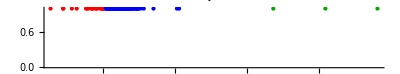
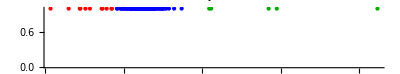
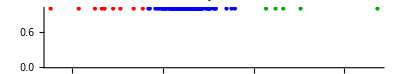
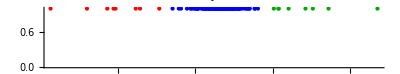

```mathematica
plots=Table[NumberLinePlot[clusterslist[[i]],PlotLegends->{"Low", "Medium", "High"},Spacings->None,PlotStyle->{Red,Blue,Darker@Green},AxesLabel->{"MSL (m)"},PlotLabel->""<>ToString[years[[i]]]<>" years"],{i,1,Length[years]}]
```

```mathematica
Table[Export["C:\\Users\\Devon\\Documents\\M3\\plots"<>ToString[i]<>".png",plots[[i]]],{i,1,Length[plots]}];
```

```mathematica
stationdata=Map[{ToExpression@#[[1]],ToExpression@#[[2]]}&,StringSplit[#,","]&/@ReadList["C:\\Users\\Devon\\Documents\\M3\\out8419870.txt",String]];
```

```mathematica
lm=LinearModelFit[stationdata,x,x]
```

FittedModel[-3.42076+0.00170302 x]

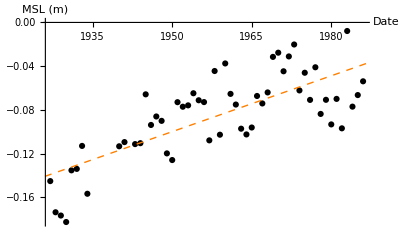

```mathematica
linearplot=Show[ListPlot[stationdata,AxesLabel->{"Date","MSL (m)"},PlotStyle->Black],Plot[lm[x],{x,1926,2010},PlotStyle->{Orange,Dashed,Thick}]]
```

```mathematica
Export["C:\\Users\\Devon\\Documents\\M3\\linearplot.png",linearplot]
```

C:\Users\Devon\Documents\M3\linearplot.png